(ⅈ ⅇ^(5 ⅈ k))/(k √(2 π))+√(π/2) DiracDelta[k]

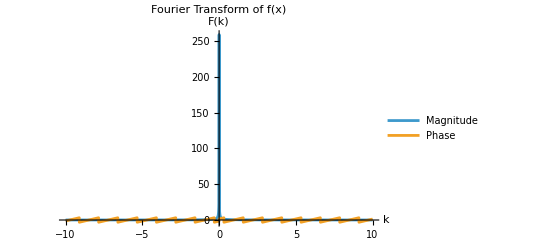

```mathematica
(*Define the function-this can be modified for other functions*)
f[x_]:=Piecewise[{{0,x<5},{1,x>=5}}]

(*Compute the Fourier transform*)
FourierTransform[f[x],x,k]

(*Plot the magnitude and phase of the Fourier transform*)
Plot[{Abs[FourierTransform[f[x],x,k]],Arg[FourierTransform[f[x],x,k]]},{k,-10,10},PlotRange->All,PlotLegends->{"Magnitude","Phase"},AxesLabel->{"k","F(k)"},PlotLabel->"Fourier Transform of f(x)"]
```

√(2 π) DiracDelta[k]

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{-∞,∞}}. NIntegrate obtained 3.58099×10^306+0. ⅈ and 6.57623×10^306 for the integral and error estimates.

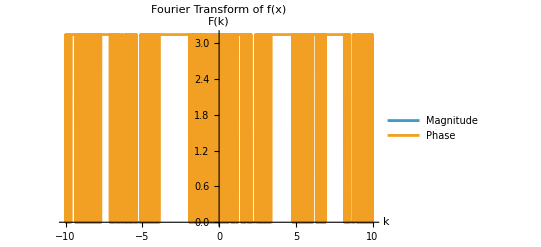

```mathematica
(*Define the function-this can be modified for other functions*)
f[x_]:=1

(*Compute the Fourier transform*)
FourierTransform[f[x],x,k]

(*Plot the magnitude and phase of the Fourier transform*)
Plot[{Abs[FourierTransform[f[x],x,k]],Arg[FourierTransform[f[x],x,k]]},{k,-10,10},PlotRange->All,PlotLegends->{"Magnitude","Phase"},AxesLabel->{"k","F(k)"},PlotLabel->"Fourier Transform of f(x)"]
```